```mathematica
<<"Turtle`"
```

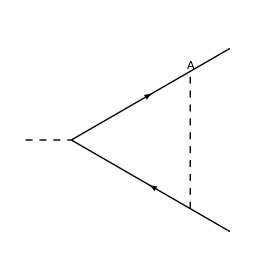

```mathematica
Graphics[{
ParseDirectives[{
"echo"["Dashed"],"Forward"[.5],"echo"["Dashing[None]"], (* Horizontal dashed line *)
{
"turn"[30°],
{"forward"[1],"Arrow"[]}, (* Arrow *)
{"forward"[1.5],"mark"["A"], "Text"["A",{0,-1}]}, (* Mark point A *)
"Forward"[2] (* Upper solid line *)
},
{
"turn"[-30°],
{"forward"[1],"turn"[180°],"Arrow"[]}, (* Arrow *)
{"forward"[1.5],"echo"["Dashed"],"Goto"["A",1],"echo"["Dashing[None]"]}, (* Vertical dashed line *)
"Forward"[2] (* Lower solid line *)
}
}]
},PlotRange->{{0,2.5},{-1.25,1.25}}]
```

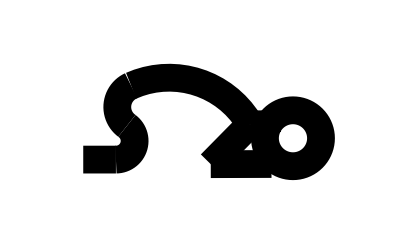

```mathematica
Graphics[{
Thickness[0.05],
ParseDirectives[{
"Forward"[0.7],
"Bend"[(4π)/5,0.4],
"Bend"[-4/6 π,0.5],
"Bend"[-1.4/3 π,2],
{
"turn"[-1.3],
"Forward"[1.2],
"turn"[2.35],
"Forward"[1.3]
},
{
"turn"[(1π)/3],
"Forward"[0.4],
"turn"[π/3],
"Bend"[-2π,0.6]
}
}]
},PlotRange->{{-1,6},{-1,3}}]
```